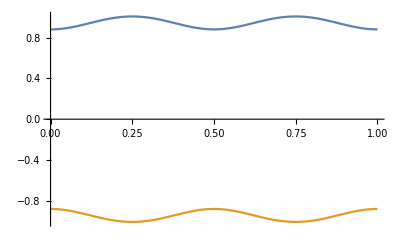

```mathematica
t0=1;
h0=0.5 t0;
a0=0.2 t0;
k=1;
Plot[{√((h0)^2(Sin[2Pi t])^2+(a0)^2(Cos[2Pi t])^2(Sin[k/2])^2+(t0)^2(Cos[k/2])^2),-√((h0)^2(Sin[2Pi t])^2+(a0)^2(Cos[2Pi t])^2(Sin[k/2])^2+(t0)^2(Cos[k/2])^2)},{t,0,1}]
```

```mathematica
Clear[k]
```

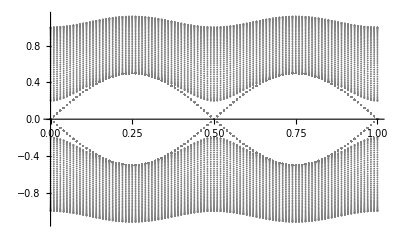

```mathematica
t0=1;
h0=0.5;
a0=0.2;
plist[k_]:=Table[√((h0)^2(Sin[2Pi t])^2+(a0)^2(Cos[2Pi t])^2(Sin[k/2])^2+(t0)^2(Cos[k/2])^2),{t,0,1,0.01}];
plist1=Table[plist[k],{k,-Pi,Pi,(2Pi)/100}];
Clear[t0,a0,h0];
t0=0;
a0=0;
h0=0.5;
plist2=Table[plist[k],{k,-Pi,Pi,(2Pi)/100}];
p1=ListPlot[plist1,PlotStyle->Gray,DataRange->{0,1}];
p2=ListPlot[-plist1,PlotStyle->Gray,DataRange->{0,1}];
p3=ListPlot[plist2,PlotStyle->Gray,DataRange->{0,1}];
p4=ListPlot[-plist2,PlotStyle->Gray,DataRange->{0,1}];
Show[{p1,p2,p3,p4},PlotRange->All]
```

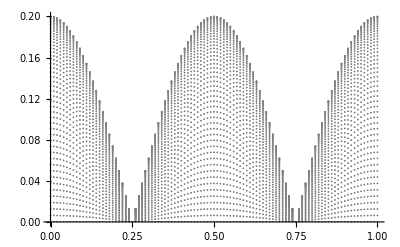

```mathematica
Clear[t0,a0,h0];
t0=0;
a0=0.2;
h0=0;
plist3=Table[plist[k],{k,-Pi,Pi,2 Pi/100}];
p5=ListPlot[plist3,PlotStyle->Gray,DataRange->{0,1}]
```

```mathematica
count1=Table[{t,√((h0)^2(Sin[2Pi t])^2+(a0)^2(Cos[2Pi t])^2(Sin[k/2])^2+(t0)^2(Cos[k/2])^2)},{t,0,1,0.01},{k,0,2Pi,2 Pi/100}];
count2=Table[{t,-√((h0)^2(Sin[2Pi t])^2+(a0)^2(Cos[2Pi t])^2(Sin[k/2])^2+(t0)^2(Cos[k/2])^2)},{t,0,1,0.01},{k,0,2Pi,2 Pi/100}];
```

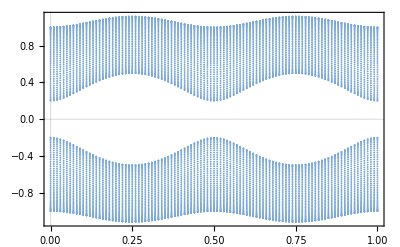

```mathematica
m1=ListPlot[count1,PlotStyle->RGBColor[0.48,0.66,0.86],PlotTheme->"Scientific"];
m2=ListPlot[count2,PlotStyle->RGBColor[0.48,0.66,0.86],PlotTheme->"Scientific"];
Show[{m1,m2},PlotRange->All,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
Export["fig1.pdf",%]
```

fig1.pdf

```mathematica
Clear[t]
matH=IdentityMatrix[20];
For[i=1,i≤20,i++,matH[[i,i]]=(-1)^i h0 Sin[2Pi t]];
For[i=1,i≤19,i++,matH[[i,i+1]]=1/2(t0+(-1)^i a0 Cos[2Pi t])];
For[i=1,i≤19,i++,matH[[i+1,i]]=1/2(t0+(-1)^i a0 Cos[2Pi t])];
```

```mathematica
Clear[matT];
matH
```

```mathematica
matT[t_]:={{-0.5 Sin[2 π t],1/2 (1-0.2 Cos[2 π t]),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2 (1-0.2 Cos[2 π t]),0.5 Sin[2 π t],1/2 (1+0.2 Cos[2 π t]),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/2 (1+0.2 Cos[2 π t]),-0.5 Sin[2 π t],1/2 (1-0.2 Cos[2 π t]),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/2 (1-0.2 Cos[2 π t]),0.5 Sin[2 π t],1/2 (1+0.2 Cos[2 π t]),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/2 (1+0.2 Cos[2 π t]),-0.5 Sin[2 π t],1/2 (1-0.2 Cos[2 π t]),0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/2 (1-0.2 Cos[2 π t]),0.5 Sin[2 π t],1/2 (1+0.2 Cos[2 π t]),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/2 (1+0.2 Cos[2 π t]),-0.5 Sin[2 π t],1/2 (1-0.2 Cos[2 π t]),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1/2 (1-0.2 Cos[2 π t]),0.5 Sin[2 π t],1/2 (1+0.2 Cos[2 π t]),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1/2 (1+0.2 Cos[2 π t]),-0.5 Sin[2 π t],1/2 (1-0.2 Cos[2 π t]),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/2 (1-0.2 Cos[2 π t]),0.5 Sin[2 π t],1/2 (1+0.2 Cos[2 π t]),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1/2 (1+0.2 Cos[2 π t]),-0.5 Sin[2 π t],1/2 (1-0.2 Cos[2 π t]),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1/2 (1-0.2 Cos[2 π t]),0.5 Sin[2 π t],1/2 (1+0.2 Cos[2 π t]),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1/2 (1+0.2 Cos[2 π t]),-0.5 Sin[2 π t],1/2 (1-0.2 Cos[2 π t]),0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/2 (1-0.2 Cos[2 π t]),0.5 Sin[2 π t],1/2 (1+0.2 Cos[2 π t]),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (1+0.2 Cos[2 π t]),-0.5 Sin[2 π t],1/2 (1-0.2 Cos[2 π t]),0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (1-0.2 Cos[2 π t]),0.5 Sin[2 π t],1/2 (1+0.2 Cos[2 π t]),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (1+0.2 Cos[2 π t]),-0.5 Sin[2 π t],1/2 (1-0.2 Cos[2 π t]),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (1-0.2 Cos[2 π t]),0.5 Sin[2 π t],1/2 (1+0.2 Cos[2 π t]),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (1+0.2 Cos[2 π t]),-0.5 Sin[2 π t],1/2 (1-0.2 Cos[2 π t])},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2 (1-0.2 Cos[2 π t]),0.5 Sin[2 π t]}};
```

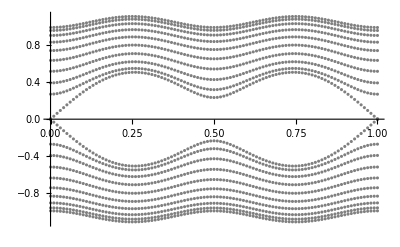

```mathematica
matE=Table[Eigenvalues[matT[t]],{t,0,1,0.01}];
ListPlot[Transpose[matE],PlotRange->All,DataRange->{0,1},PlotStyle->Gray]
```